### Gell - Mann Matrix representation of SU (3)

```mathematica
λ1={{0,1,0},{1,0,0},{0,0,0}};
λ2={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}};
λ3={{1,0,0},{0,-1,0},{0,0,0}};
λ4={{0,0,1},{0,0,0},{1,0,0}};
λ5={{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}};
λ6={{0,0,0},{0,0,1},{0,1,0}};
λ7={{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}};
λ8={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];
```

### F - spin representation of SU (3)

```mathematica
F1= λ1/2;
F2= λ2/2;
F3= λ3/2;
F4= λ4/2;
F5= λ5/2;
F6= λ6/2;
F7= λ7/2;
F8= λ8/2;
```

```mathematica
Y=2F8 / Sqrt[3];

Iplus=F1+ ⅈ F2;
Iminus=F1- ⅈ F2;
I0=F3;

Vplus=F4+ ⅈ F5;
Vminus=F4- ⅈ F5;
V0= (Vplus.Vminus-Vminus.Vplus)/2;

Uplus=F6+ ⅈ F7;
Uminus=F6- ⅈ F7;
U0= (Uplus.Uminus-Uminus.Uplus)/2;
```

#### Here we define a function which can calulate the matrix governing the system of differential equations

```mathematica
GetHamiltonian[list_]:=(s=0;Do[w= D[Part[list,iterator2,1],z]*IdentityMatrix[3];Do[w=w.Evaluate[MatrixExp[ Part[list,iterator1,1]*Part[list,iterator1,2]]],{iterator1,iterator2-1}];
w= w.Part[list,iterator2,2];Do[w=w.Evaluate[MatrixExp[-Part[list,iterator2-iterator1,1]*Part[list,iterator2-iterator1,2]]],{iterator1,iterator2-1}];s=s+w,{iterator2,Length[list]}];Return[s]);
GetPropagator[list_]:=(
w=IdentityMatrix[3];
Do[w=w.MatrixExp[ Part[list,iterator,1]*Part[list,iterator,2]],{iterator,Length[list]}];
Return[w]
);
```

```mathematica
list =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{ⅈ  ι0[z],I0},{ⅈ  y0[z],Y},{ⅈ  ey[z],IdentityMatrix[3]},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];
listOfFunctions = {ιp[z], μp[z],  νp[z],
ι0[z],y0[z],ey[z],
νm[z], μm[z], ιm[z]}
listOfDerivatives=D[#,z]&/@listOfFunctions
```

{ιp[z],μp[z],νp[z],ι0[z],y0[z],ey[z],νm[z],μm[z],ιm[z]}

{ιp'[z],μp'[z],νp'[z],ι0'[z],y0'[z],ey'[z],νm'[z],μm'[z],ιm'[z]}

```mathematica
(res=FullSimplify[GetHamiltonian[list]]);
H=({{ω1[z], g01[z], g02[z]}, {g01[z], ω2[z], g12[z]}, {g02[z], g12[z], 0}});
eqs=Thread[(Flatten[res]==Flatten[ ⅈ H])];
sol=FullSimplify[Solve[eqs,listOfDerivatives]];
eqs1=Thread[listOfDerivatives==((listOfDerivatives/.sol)[[1]])];
```

```mathematica
sol//TraditionalForm
eqs1//TraditionalForm
```

{{ιp'(z)→g01(z) ((ιp(z))^2+1)-ⅈ (g12(z) νp(z)+ιp(z) (ⅈ g02(z) νp(z)-ω1(z)+ω2(z))),μp'(z)→-(g01(z)-ⅈ g02(z) μp(z)) (ιp(z) μp(z)-ⅈ νp(z))+g12(z) ((μp(z))^2+1)+ⅈ μp(z) ω2(z),νp'(z)→νp(z) (g01(z) ιp(z)+ⅈ ω1(z))+g02(z) ((νp(z))^2+1)-ⅈ g12(z) ιp(z),ι0'(z)→-2 ⅈ g01(z) ιp(z)-g02(z) (ιp(z) μp(z)+ⅈ νp(z))+ⅈ g12(z) μp(z)+ω1(z)-ω2(z),y0'(z)→1/2 (-3 ⅈ (g12(z) μp(z)+g02(z) (νp(z)+ⅈ ιp(z) μp(z)))+ω1(z)+ω2(z)),ey'(z)→1/3 (ω1(z)+ω2(z)),νm'(z)→g02(z) ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z)))-ⅈ ⅇ^(ⅈ ι0(z)) μm(z) (g01(z)-ⅈ g02(z) μp(z)),μm'(z)→ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)),ιm'(z)→ⅇ^(ⅈ ι0(z)) (g01(z)-ⅈ g02(z) μp(z))}}

{ιp'(z)==g01(z) ((ιp(z))^2+1)-ⅈ (g12(z) νp(z)+ιp(z) (ⅈ g02(z) νp(z)-ω1(z)+ω2(z))),μp'(z)==-(g01(z)-ⅈ g02(z) μp(z)) (ιp(z) μp(z)-ⅈ νp(z))+g12(z) ((μp(z))^2+1)+ⅈ μp(z) ω2(z),νp'(z)==νp(z) (g01(z) ιp(z)+ⅈ ω1(z))+g02(z) ((νp(z))^2+1)-ⅈ g12(z) ιp(z),ι0'(z)==-2 ⅈ g01(z) ιp(z)-g02(z) (ιp(z) μp(z)+ⅈ νp(z))+ⅈ g12(z) μp(z)+ω1(z)-ω2(z),y0'(z)==1/2 (-3 ⅈ (g12(z) μp(z)+g02(z) (νp(z)+ⅈ ιp(z) μp(z)))+ω1(z)+ω2(z)),ey'(z)==1/3 (ω1(z)+ω2(z)),νm'(z)==g02(z) ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z)))-ⅈ ⅇ^(ⅈ ι0(z)) μm(z) (g01(z)-ⅈ g02(z) μp(z)),μm'(z)==ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)),ιm'(z)==ⅇ^(ⅈ ι0(z)) (g01(z)-ⅈ g02(z) μp(z))}

```mathematica
Table[{FullSimplify[eqs1[[j]]]},{j,1,8}] //TraditionalForm
```

(g01(z) ((ιp(z))^2+1)-ⅈ g12(z) νp(z)+ιp(z) (g02(z) νp(z)+ⅈ (ω1(z)-ω2(z)))==ιp'(z)
g12(z) ((μp(z))^2+1)+ⅈ μp(z) ω2(z)==(g01(z)-ⅈ g02(z) μp(z)) (ιp(z) μp(z)-ⅈ νp(z))+μp'(z)
ⅈ g12(z) ιp(z)+νp'(z)==g02(z) ((νp(z))^2+1)+νp(z) (g01(z) ιp(z)+ⅈ ω1(z))
2 ⅈ g01(z) ιp(z)+g02(z) μp(z) ιp(z)-ⅈ g12(z) μp(z)+ⅈ g02(z) νp(z)+ω2(z)+ι0'(z)==ω1(z)
3 ⅈ (g12(z) μp(z)+g02(z) νp(z))+2 y0'(z)==3 g02(z) ιp(z) μp(z)+ω1(z)+ω2(z)
ω1(z)+ω2(z)==3 ey'(z)
ⅇ^(ⅈ ι0(z)) μm(z) (ⅈ g01(z)+g02(z) μp(z))+νm'(z)==ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z))) g02(z)
μm'(z)==ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)))

```mathematica
ode = Join[eqs1,{ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,y0[0]==0,νm[0]==0,μp[0]==0,μm[0]==0}];
```

```mathematica
sol = NDSolve[ode/.{g01[z]->1,g02[z]->1,g12[z]->1},listOfFunctions,{z,0,15}]
```

{{ιp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ι0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],y0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ιm[z]→InterpolatingFunction[{{0., 15.}}, <>][z]}}

```mathematica
ss=FullSimplify[D[GetPropagator[list],z].Inverse[GetPropagator[list]]]//TraditionalForm
```

(1/6 ⅈ (2 y0'(z)+3 ι0'(z))-ⅇ^(-ⅈ ι0(z)) ιp(z) ιm'(z)+ⅇ^(-1/2 ⅈ (2 y0(z)+ι0(z))) (ιp(z) μp(z)-ⅈ νp(z)) (μm(z) ιm'(z)-ⅈ νm'(z)) | ⅇ^(-ⅈ ι0(z)) (ⅈ ιm'(z) (ιp(z))^2+ⅇ^(ⅈ ι0(z)) ι0'(z) ιp(z)+ⅈ ⅇ^(ⅈ ι0(z)) ιp'(z)-ⅈ ⅇ^(1/2 ⅈ ι0(z)-ⅈ y0(z)) (ιp(z) μp(z)-ⅈ νp(z)) (ⅇ^(ⅈ ι0(z)) μm'(z)+ιp(z) (μm(z) ιm'(z)-ⅈ νm'(z)))) | 1/2 (2 ⅈ ιp(z) μp(z) y0'(z)+2 νp(z) y0'(z)-ⅈ ιp(z) μp(z) ι0'(z)+νp(z) ι0'(z)+2 ⅈ ⅇ^(-ⅈ ι0(z)) ιp(z) νp(z) ιm'(z)-2 ⅇ^(1/2 ⅈ ι0(z)-ⅈ y0(z)) μp(z) (ιp(z) μp(z)-ⅈ νp(z)) μm'(z)-2 ιp(z) μp'(z)-2 ⅇ^(-1/2 ⅈ (2 y0(z)+ι0(z))) νp(z) (ⅈ ιp(z) μp(z)+νp(z)) (μm(z) ιm'(z)-ⅈ νm'(z))+2 ⅈ νp'(z))
ⅈ ⅇ^(-ⅈ ι0(z)) (ιm'(z)+ⅇ^(1/2 ⅈ ι0(z)-ⅈ y0(z)) μp(z) (ⅈ νm'(z)-μm(z) ιm'(z))) | 1/3 ⅈ y0'(z)-1/2 ⅈ ι0'(z)+ⅇ^(-ⅈ (y0(z)+ι0(z))) (ⅇ^(ⅈ y0(z)) ιp(z) ιm'(z)-ⅇ^(1/2 ⅈ ι0(z)) μp(z) (ⅇ^(ⅈ ι0(z)) μm'(z)+ιp(z) (μm(z) ιm'(z)-ⅈ νm'(z)))) | ⅈ ⅇ^(1/2 ⅈ ι0(z)-ⅈ y0(z)) μm'(z) (μp(z))^2+1/2 (2 y0'(z)-ι0'(z)-2 ⅇ^(-1/2 ⅈ (2 y0(z)+ι0(z))) νp(z) (μm(z) ιm'(z)-ⅈ νm'(z))) μp(z)+ⅇ^(-ⅈ ι0(z)) νp(z) ιm'(z)+ⅈ μp'(z)
ⅇ^(-1/2 ⅈ (2 y0(z)+ι0(z))) (ⅈ νm'(z)-μm(z) ιm'(z)) | ⅇ^(-1/2 ⅈ (2 y0(z)+ι0(z))) (ⅈ ⅇ^(ⅈ ι0(z)) μm'(z)+ιp(z) (ⅈ μm(z) ιm'(z)+νm'(z))) | ⅇ^(-1/2 ⅈ (2 y0(z)+ι0(z))) (ⅇ^(ⅈ ι0(z)) μp(z) μm'(z)+νp(z) (ⅈ μm(z) ιm'(z)+νm'(z)))-2/3 ⅈ y0'(z))

```mathematica
N[MatrixExp[ 1.0ⅈ ({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}})]]//TraditionalForm
```

(0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ)

```mathematica
(GetPropagator[list ]/.sol/.{z->1.0})[[1]]//TraditionalForm
```

{ⅈ ιm(1.) (ⅈ ιp(1.) ⅇ^(1/3 ⅈ y0(1.)-1/2 ⅈ ι0(1.))+ⅈ μm(1.) ⅇ^(-2/3 ⅈ y0(1.)) (-ιp(1.) μp(1.)+ⅈ νp(1.)))+ⅇ^(1/2 ⅈ ι0(1.)+1/3 ⅈ y0(1.))+ⅈ νm(1.) ⅇ^(-2/3 ⅈ y0(1.)) (-ιp(1.) μp(1.)+ⅈ νp(1.)),ⅈ ιp(1.) ⅇ^(1/3 ⅈ y0(1.)-1/2 ⅈ ι0(1.))+ⅈ μm(1.) ⅇ^(-2/3 ⅈ y0(1.)) (-ιp(1.) μp(1.)+ⅈ νp(1.)),ⅇ^(-2/3 ⅈ y0(1.)) (-ιp(1.) μp(1.)+ⅈ νp(1.))}

```mathematica
Chop[ss/.sol/.D[sol,z]/.{z->.000001}]
```

(1/6 ⅈ (2 y0'(1.×10^-6)+3 ι0'(1.×10^-6))-ⅇ^(-ⅈ ι0(1.×10^-6)) ιp(1.×10^-6) ιm'(1.×10^-6)+ⅇ^(-1/2 ⅈ (2 y0(1.×10^-6)+ι0(1.×10^-6))) (ιp(1.×10^-6) μp(1.×10^-6)-ⅈ νp(1.×10^-6)) (μm(1.×10^-6) ιm'(1.×10^-6)-ⅈ νm'(1.×10^-6)) | ⅇ^(-ⅈ ι0(1.×10^-6)) (ⅈ ιm'(1.×10^-6) (ιp(1.×10^-6))^2+ⅇ^(ⅈ ι0(1.×10^-6)) ι0'(1.×10^-6) ιp(1.×10^-6)+ⅈ ⅇ^(ⅈ ι0(1.×10^-6)) ιp'(1.×10^-6)-ⅈ ⅇ^(1/2 ⅈ ι0(1.×10^-6)-ⅈ y0(1.×10^-6)) (ιp(1.×10^-6) μp(1.×10^-6)-ⅈ νp(1.×10^-6)) (ⅇ^(ⅈ ι0(1.×10^-6)) μm'(1.×10^-6)+ιp(1.×10^-6) (μm(1.×10^-6) ιm'(1.×10^-6)-ⅈ νm'(1.×10^-6)))) | 1/2 (2 ⅈ ιp(1.×10^-6) μp(1.×10^-6) y0'(1.×10^-6)+2 νp(1.×10^-6) y0'(1.×10^-6)-ⅈ ιp(1.×10^-6) μp(1.×10^-6) ι0'(1.×10^-6)+νp(1.×10^-6) ι0'(1.×10^-6)+2 ⅈ ⅇ^(-ⅈ ι0(1.×10^-6)) ιp(1.×10^-6) νp(1.×10^-6) ιm'(1.×10^-6)-2 ⅇ^(1/2 ⅈ ι0(1.×10^-6)-ⅈ y0(1.×10^-6)) μp(1.×10^-6) (ιp(1.×10^-6) μp(1.×10^-6)-ⅈ νp(1.×10^-6)) μm'(1.×10^-6)-2 ιp(1.×10^-6) μp'(1.×10^-6)-2 ⅇ^(-1/2 ⅈ (2 y0(1.×10^-6)+ι0(1.×10^-6))) νp(1.×10^-6) (ⅈ ιp(1.×10^-6) μp(1.×10^-6)+νp(1.×10^-6)) (μm(1.×10^-6) ιm'(1.×10^-6)-ⅈ νm'(1.×10^-6))+2 ⅈ νp'(1.×10^-6))
ⅈ ⅇ^(-ⅈ ι0(1.×10^-6)) (ιm'(1.×10^-6)+ⅇ^(1/2 ⅈ ι0(1.×10^-6)-ⅈ y0(1.×10^-6)) μp(1.×10^-6) (ⅈ νm'(1.×10^-6)-μm(1.×10^-6) ιm'(1.×10^-6))) | 1/3 ⅈ y0'(1.×10^-6)-1/2 ⅈ ι0'(1.×10^-6)+ⅇ^(-ⅈ (y0(1.×10^-6)+ι0(1.×10^-6))) (ⅇ^(ⅈ y0(1.×10^-6)) ιp(1.×10^-6) ιm'(1.×10^-6)-ⅇ^(1/2 ⅈ ι0(1.×10^-6)) μp(1.×10^-6) (ⅇ^(ⅈ ι0(1.×10^-6)) μm'(1.×10^-6)+ιp(1.×10^-6) (μm(1.×10^-6) ιm'(1.×10^-6)-ⅈ νm'(1.×10^-6)))) | ⅈ ⅇ^(1/2 ⅈ ι0(1.×10^-6)-ⅈ y0(1.×10^-6)) μm'(1.×10^-6) (μp(1.×10^-6))^2+1/2 (2 y0'(1.×10^-6)-ι0'(1.×10^-6)-2 ⅇ^(-1/2 ⅈ (2 y0(1.×10^-6)+ι0(1.×10^-6))) νp(1.×10^-6) (μm(1.×10^-6) ιm'(1.×10^-6)-ⅈ νm'(1.×10^-6))) μp(1.×10^-6)+ⅇ^(-ⅈ ι0(1.×10^-6)) νp(1.×10^-6) ιm'(1.×10^-6)+ⅈ μp'(1.×10^-6)
ⅇ^(-1/2 ⅈ (2 y0(1.×10^-6)+ι0(1.×10^-6))) (ⅈ νm'(1.×10^-6)-μm(1.×10^-6) ιm'(1.×10^-6)) | ⅇ^(-1/2 ⅈ (2 y0(1.×10^-6)+ι0(1.×10^-6))) (ⅈ ⅇ^(ⅈ ι0(1.×10^-6)) μm'(1.×10^-6)+ιp(1.×10^-6) (ⅈ μm(1.×10^-6) ιm'(1.×10^-6)+νm'(1.×10^-6))) | ⅇ^(-1/2 ⅈ (2 y0(1.×10^-6)+ι0(1.×10^-6))) (ⅇ^(ⅈ ι0(1.×10^-6)) μp(1.×10^-6) μm'(1.×10^-6)+νp(1.×10^-6) (ⅈ μm(1.×10^-6) ιm'(1.×10^-6)+νm'(1.×10^-6)))-2/3 ⅈ y0'(1.×10^-6))

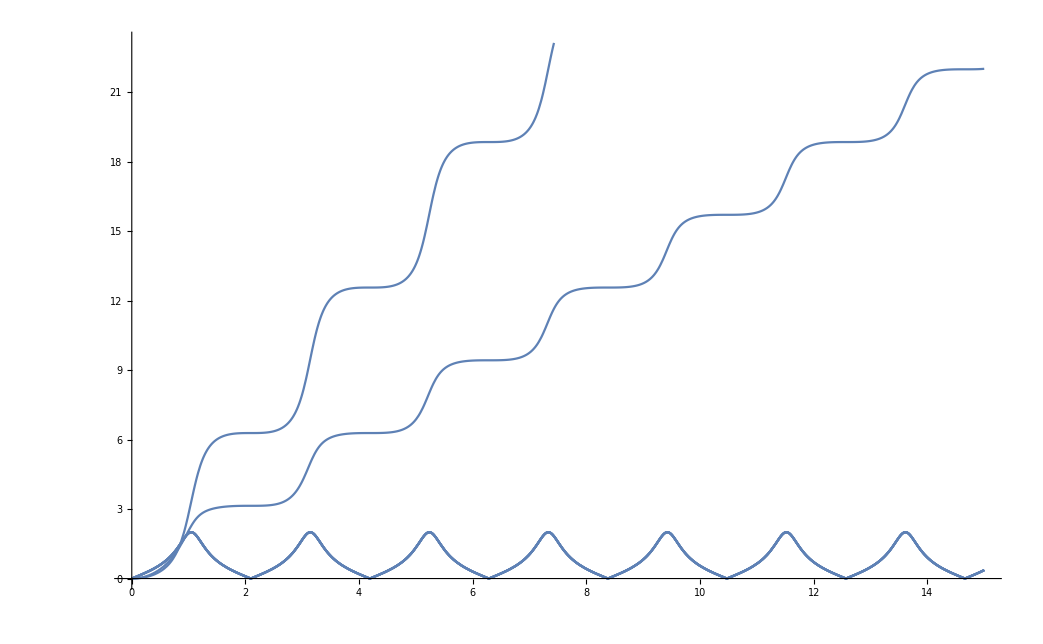

```mathematica
Plot[{ Abs[ιp[z]], Abs[ι0[z]], Abs[ιm[z]],Abs[νp[z]], Abs[y0[z]],Abs[νm[z]],Abs[μp[z]],Abs[μm[z]]}/.sol,{z,0,15}]
```

#### With Logarithms

```mathematica
list =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{Log[ ι0[z]],I0},{Log[ y0[z]],Y},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];
listOfFunctions = {ιp[z], μp[z],  νp[z],
ι0[z],y0[z],
νm[z], μm[z], ιm[z]}
listOfDerivatives=D[#,z]&/@listOfFunctions
```

{ιp[z],μp[z],νp[z],ι0[z],y0[z],νm[z],μm[z],ιm[z]}

{ιp'[z],μp'[z],νp'[z],ι0'[z],y0'[z],νm'[z],μm'[z],ιm'[z]}

```mathematica
(res=FullSimplify[GetHamiltonian[list]]);
H=({{0, g01[z], g02[z]}, {g01[z], 0, g12[z]}, {g02[z], g12[z], 0}});
eqs=Thread[(Flatten[res]==Flatten[ ⅈ H])];
sol=FullSimplify[Solve[eqs,listOfDerivatives]];
eqs1=Thread[listOfDerivatives==((listOfDerivatives/.sol)[[1]])];
```

```mathematica
sol//TraditionalForm
eqs1//TraditionalForm
eqs1
```

{{ιp'(z)→g01(z) ((ιp(z))^2+1)+νp(z) (g02(z) ιp(z)-ⅈ g12(z)),μp'(z)→g12(z) ((μp(z))^2+1)-(g01(z)-ⅈ g02(z) μp(z)) (ιp(z) μp(z)-ⅈ νp(z)),νp'(z)→g02(z) ((νp(z))^2+1)+ιp(z) (g01(z) νp(z)-ⅈ g12(z)),ι0'(z)→ι0(z) (2 g01(z) ιp(z)-μp(z) (g12(z)+ⅈ g02(z) ιp(z))+g02(z) νp(z)),y0'(z)→3/2 y0(z) (g12(z) μp(z)+g02(z) (νp(z)+ⅈ ιp(z) μp(z))),νm'(z)→g02(z) (y0(z) √(ι0(z))-ι0(z) μm(z) μp(z))-ⅈ g01(z) ι0(z) μm(z),μm'(z)→(y0(z) (g12(z)+ⅈ g02(z) ιp(z)))/(√(ι0(z))),ιm'(z)→ι0(z) (g01(z)-ⅈ g02(z) μp(z))}}

{ιp'(z)==g01(z) ((ιp(z))^2+1)+νp(z) (g02(z) ιp(z)-ⅈ g12(z)),μp'(z)==g12(z) ((μp(z))^2+1)-(g01(z)-ⅈ g02(z) μp(z)) (ιp(z) μp(z)-ⅈ νp(z)),νp'(z)==g02(z) ((νp(z))^2+1)+ιp(z) (g01(z) νp(z)-ⅈ g12(z)),ι0'(z)==ι0(z) (2 g01(z) ιp(z)-μp(z) (g12(z)+ⅈ g02(z) ιp(z))+g02(z) νp(z)),y0'(z)==3/2 y0(z) (g12(z) μp(z)+g02(z) (νp(z)+ⅈ ιp(z) μp(z))),νm'(z)==g02(z) (y0(z) √(ι0(z))-ι0(z) μm(z) μp(z))-ⅈ g01(z) ι0(z) μm(z),μm'(z)==(y0(z) (g12(z)+ⅈ g02(z) ιp(z)))/(√(ι0(z))),ιm'(z)==ι0(z) (g01(z)-ⅈ g02(z) μp(z))}

{ιp'[z]==g01[z] (1+ιp[z]^2)+(-ⅈ g12[z]+g02[z] ιp[z]) νp[z],μp'[z]==g12[z] (1+μp[z]^2)-(g01[z]-ⅈ g02[z] μp[z]) (ιp[z] μp[z]-ⅈ νp[z]),νp'[z]==ιp[z] (-ⅈ g12[z]+g01[z] νp[z])+g02[z] (1+νp[z]^2),ι0'[z]==ι0[z] (2 g01[z] ιp[z]-(g12[z]+ⅈ g02[z] ιp[z]) μp[z]+g02[z] νp[z]),y0'[z]==3/2 y0[z] (g12[z] μp[z]+g02[z] (ⅈ ιp[z] μp[z]+νp[z])),νm'[z]==-ⅈ g01[z] ι0[z] μm[z]+g02[z] (y0[z] √ι0[z]-ι0[z] μm[z] μp[z]),μm'[z]==(y0[z] (g12[z]+ⅈ g02[z] ιp[z]))/(√ι0[z]),ιm'[z]==ι0[z] (g01[z]-ⅈ g02[z] μp[z])}

```mathematica
ode = Join[eqs1,{ιp[0]==0,ι0[0]==1,ιm[0]==0,νp[0]==0,y0[0]==1,νm[0]==0,μp[0]==0,μm[0]==0}];
```

```mathematica
sol = NDSolve[ode/.{g01[z]->1,g02[z]->1,g12[z]->1},listOfFunctions,{z,0,15}]
```

{{ιp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ι0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],y0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ιm[z]→InterpolatingFunction[{{0., 15.}}, <>][z]}}

```mathematica
ss=FullSimplify[D[GetPropagator[list],z].Inverse[GetPropagator[list]]]//TraditionalForm
```

((2 ι0(z) y0'(z)+3 y0(z) (ι0'(z)-2 ιp(z) ιm'(z))+6 √(ι0(z)) (ιp(z) μp(z)-ⅈ νp(z)) (μm(z) ιm'(z)-ⅈ νm'(z)))/(6 y0(z) ι0(z)) | (ⅈ (y0(z) (ιm'(z) (ιp(z))^2-ι0'(z) ιp(z)+ι0(z) ιp'(z))-√(ι0(z)) (ιp(z) μp(z)-ⅈ νp(z)) (ι0(z) μm'(z)+ιp(z) (μm(z) ιm'(z)-ⅈ νm'(z)))))/(y0(z) ι0(z)) | -(2 μp(z) (ιp(z) μp(z)-ⅈ νp(z)) μm'(z) (ι0(z))^(3/2)+(ιp(z) (2 y0(z) μp'(z)-2 μp(z) y0'(z))+2 ⅈ (νp(z) y0'(z)-y0(z) νp'(z))) ι0(z)+2 νp(z) (ⅈ ιp(z) μp(z)+νp(z)) (μm(z) ιm'(z)-ⅈ νm'(z)) √(ι0(z))+y0(z) ((ιp(z) μp(z)+ⅈ νp(z)) ι0'(z)-2 ⅈ ιp(z) νp(z) ιm'(z)))/(2 y0(z) ι0(z))
(ⅈ (y0(z) ιm'(z)+√(ι0(z)) μp(z) (ⅈ νm'(z)-μm(z) ιm'(z))))/(y0(z) ι0(z)) | -(6 μp(z) μm'(z) (ι0(z))^(3/2)-2 y0'(z) ι0(z)+6 ιp(z) μp(z) (μm(z) ιm'(z)-ⅈ νm'(z)) √(ι0(z))+3 y0(z) (ι0'(z)-2 ιp(z) ιm'(z)))/(6 y0(z) ι0(z)) | (ⅈ (2 (ι0(z))^(3/2) μm'(z) (μp(z))^2+2 √(ι0(z)) νp(z) (ⅈ μm(z) ιm'(z)+νm'(z)) μp(z)+y0(z) (μp(z) ι0'(z)-2 ⅈ νp(z) ιm'(z))+ι0(z) (2 y0(z) μp'(z)-2 μp(z) y0'(z))))/(2 y0(z) ι0(z))
(ⅈ νm'(z)-μm(z) ιm'(z))/(y0(z) √(ι0(z))) | (ⅈ ι0(z) μm'(z)+ιp(z) (ⅈ μm(z) ιm'(z)+νm'(z)))/(y0(z) √(ι0(z))) | (-2 √(ι0(z)) y0'(z)+3 ι0(z) μp(z) μm'(z)+3 νp(z) (ⅈ μm(z) ιm'(z)+νm'(z)))/(3 y0(z) √(ι0(z))))

```mathematica
N[MatrixExp[ 1.0ⅈ ({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}})]]//TraditionalForm
```

(0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ)

```mathematica
(GetPropagator[list ]/.sol/.{z->1.0})[[1]]//TraditionalForm
```

(0.221485-0.257881 ⅈ | -0.318817+0.583589 ⅈ | -0.318816+0.583589 ⅈ
-0.318817+0.583589 ⅈ | 0.221486-0.257882 ⅈ | -0.318816+0.58359 ⅈ
-0.318816+0.583589 ⅈ | -0.318816+0.58359 ⅈ | 0.221486-0.257882 ⅈ)

```mathematica
Chop[ss/.sol/.D[sol,z]/.{z->.000001}]
```

{{(5.94923×10^-6-9.29497×10^-10 ⅈ | 2.97462×10^-6+1. ⅈ | 2.97462×10^-6+1. ⅈ
2.97461×10^-6+1. ⅈ | 0.+1.39821×10^-9 ⅈ | -2.97461×10^-6+1. ⅈ
2.97461×10^-6+1. ⅈ | -2.97462×10^-6+1. ⅈ | -5.94923×10^-6-4.68715×10^-10 ⅈ)}}

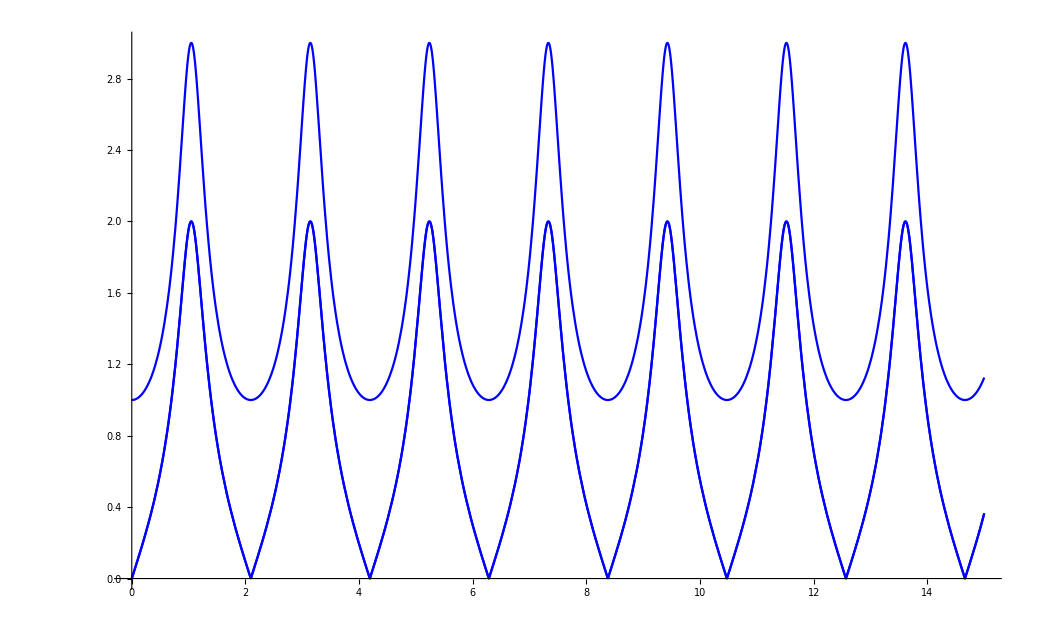

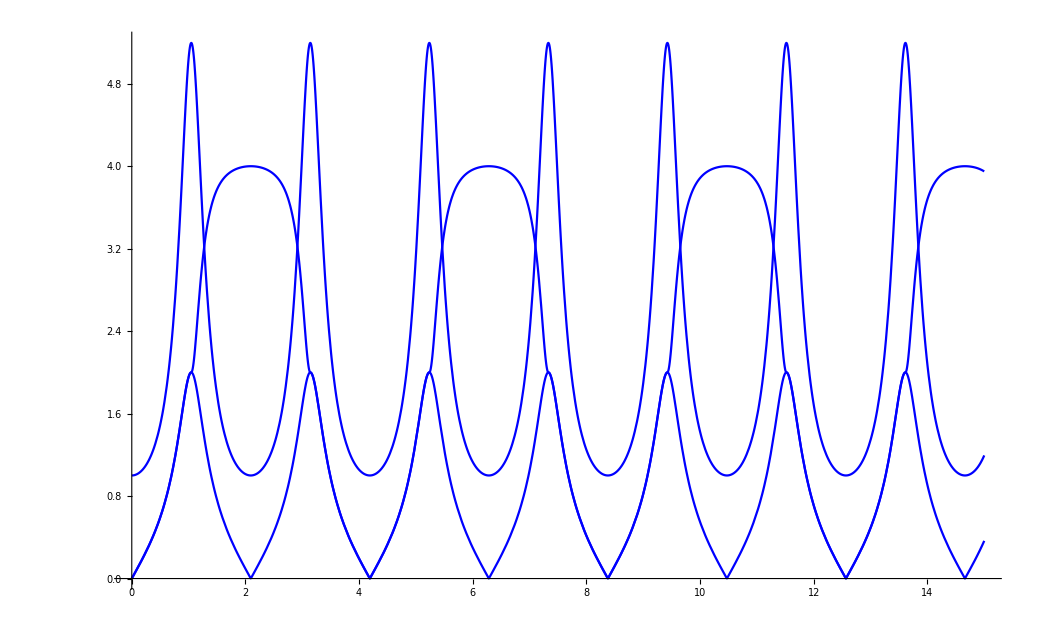

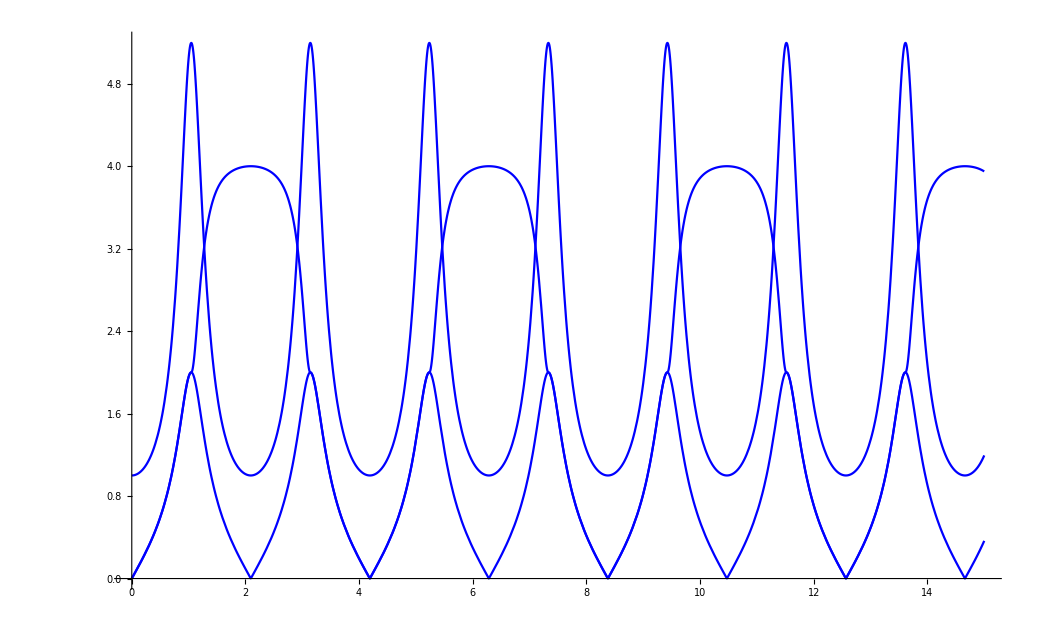

```mathematica
Plot[Flatten[{ Abs[ιp[z]], Abs[ι0[z]], Abs[ιm[z]]}/.sol],{z,0,15}, PlotStyle->{Red,Black,Blue}]
Plot[{ Abs[νp[z]], Abs[y0[z]],Abs[νm[z]]}/.sol,{z,0,15}, PlotStyle->{Red,Black,Blue}]
Plot[{ Abs[μp[z]], Abs[y0[z]],Abs[μm[z]]}/.sol,{z,0,15}, PlotStyle->{Red,Black,Blue}]
```

```mathematica
GetPropagator[list]//TraditionalForm
```

(ⅈ ιm(z) (ⅈ ⅇ^(ⅈ ey(z)+1/3 ⅈ y0(z)-1/2 ⅈ ι0(z)) ιp(z)+ⅈ ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μm(z) (ⅈ νp(z)-ιp(z) μp(z)))+ⅇ^(ⅈ ey(z)+1/3 ⅈ y0(z)+1/2 ⅈ ι0(z))+ⅈ ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) νm(z) (ⅈ νp(z)-ιp(z) μp(z)) | ⅈ ⅇ^(ⅈ ey(z)+1/3 ⅈ y0(z)-1/2 ⅈ ι0(z)) ιp(z)+ⅈ ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μm(z) (ⅈ νp(z)-ιp(z) μp(z)) | ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) (ⅈ νp(z)-ιp(z) μp(z))
ⅈ ιm(z) (ⅇ^(ⅈ ey(z)+1/3 ⅈ y0(z)-1/2 ⅈ ι0(z))-ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μm(z) μp(z))-ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μp(z) νm(z) | ⅇ^(ⅈ ey(z)+1/3 ⅈ y0(z)-1/2 ⅈ ι0(z))-ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μm(z) μp(z) | ⅈ ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μp(z)
ⅈ ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) νm(z)-ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) ιm(z) μm(z) | ⅈ ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)) μm(z) | ⅇ^(ⅈ ey(z)-2/3 ⅈ y0(z)))